```mathematica
SetDirectory[NotebookDirectory[]]
```

G:\Mi unidad\Res_Tesis\ArtificialData

```mathematica
nnoise=Import["feature_nnoise.csv"];
```

```mathematica
noise=Import["feature_noise.csv"];
```

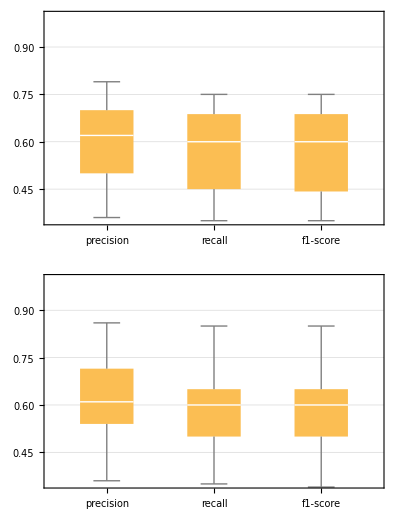

```mathematica
GraphicsGrid[{{BoxWhiskerChart[nnoise[[;;,;;]]ᵀ, ChartLabels->nnoise[[1,;;]],PlotTheme->"Detailed", PlotRange->{0.35,1}]},{BoxWhiskerChart[noise[[;;,;;]]ᵀ, ChartLabels->nnoise[[1,;;]],PlotTheme->"Detailed", PlotRange->{0.35,1}]}}]
```

```mathematica
nnoise[[2;;,1]]
```

{0.66,0.5,0.76,0.64,0.52,0.5,0.76,0.56,0.76,0.36,0.5,0.43,0.68,0.65,0.66,0.43,0.73,0.43,0.79,0.7,0.46,0.7,0.61,0.44,0.62,0.62,0.76}

```mathematica
noise[[2;;,1]]
```

{0.62,0.54,0.58,0.8,0.7,0.62,0.61,0.54,0.6,0.6,0.86,0.73,0.65,0.5,0.72,0.61,0.46,0.36,0.76,0.38,0.56,0.38,0.52,0.73,0.68,0.54,0.76}

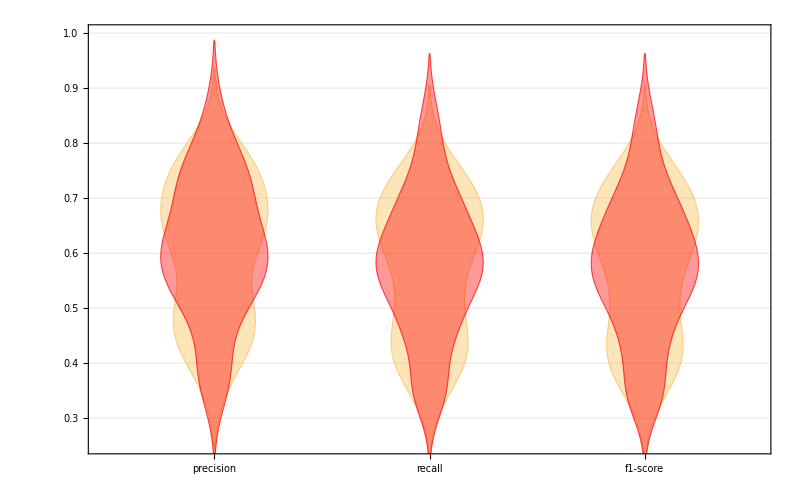

```mathematica
Show[{{DistributionChart[nnoise[[;;,;;]]ᵀ, ChartLabels->nnoise[[1,;;]],PlotTheme->"Detailed", PlotRange->{0.25,1}, ChartStyle->{Opacity[0.4]}]},{DistributionChart[noise[[;;,;;]]ᵀ, ChartLabels->nnoise[[1,;;]],PlotTheme->"Detailed", PlotRange->{0.25,1},ChartStyle->{Opacity[0.4],{Red, Red, Red}}]}}]
```

```mathematica
Needs["ANOVA`"]
```

```mathematica
ANOVA[{nnoise[[2;;,1]],noise[[2;;,1]]}ᵀ,PostTests->Bonferroni,SignificanceLevel->.01,CellMeans->False]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 16 | 0.266458 | 0.0166536 | 1.02795 | 0.498787
Error | 10 | 0.162008 | 0.0162008 |  | 
Total | 26 | 0.428467 |  |  | ,PostTests→{Model→Bonferroni | {}}}

```mathematica
Table[ANOVA[{nnoise[[2;;,i]],noise[[2;;,i]]}ᵀ,CellMeans->False],{i,1,3}]//MatrixForm
```

(ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 16 | 0.266458 | 0.0166536 | 1.02795 | 0.498787
Error | 10 | 0.162008 | 0.0162008 |  | 
Total | 26 | 0.428467 |  |  | 
ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 8 | 0.088875 | 0.0111094 | 0.574967 | 0.785105
Error | 18 | 0.347792 | 0.0193218 |  | 
Total | 26 | 0.436667 |  |  | 
ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 13 | 0.169933 | 0.0130718 | 0.58814 | 0.824686
Error | 13 | 0.288933 | 0.0222256 |  | 
Total | 26 | 0.458867 |  |  | )

```mathematica
EstimatedDistribution[nnoise[[2;;,1]],NormalDistribution[μ,σ]]
```

NormalDistribution[0.601111,0.124939]

```mathematica
EstimatedDistribution[noise[[2;;,1]],NormalDistribution[μ,σ]]
```

NormalDistribution[0.607778,0.125973]

```mathematica
AndersonDarlingTest[noise[[2;;,1]],nnoise[[2;;,1]]]
```

0.836943

```mathematica
StandardDeviation[nnoise[[2;;,1]]]
```

0.12732

```mathematica
StandardDeviation[noise[[2;;,1]]]
```

0.128372

```mathematica
Abs[StandardDeviation[nnoise[[2;;,1]]]-StandardDeviation[noise[[2;;,1]]]]^2
```

1.1087×10^-6

```mathematica
With[
{x=nnoise[[2;;,1]],
y=noise[[2;;,1]]},
KolmogorovSmirnovTest[x,y,"PValueTable"]]
```

| P-Value
Kolmogorov-Smirnov | 0.880872

```mathematica
Correlation[nnoise[[2;;,1]],noise[[2;;,1]]]
```

-0.0443187

```mathematica
ℋ1=KolmogorovSmirnovTest[nnoise[[2;;,1]],Automatic,"TestData"]
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

{0.124156,0.352829}

```mathematica
ℋ2=KolmogorovSmirnovTest[noise[[2;;,1]],Automatic,"TestData"]
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

{0.0909838,0.824789}

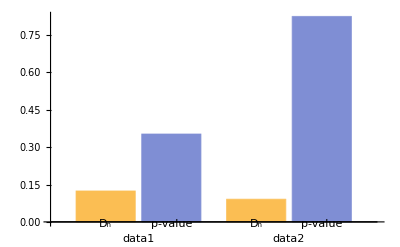

```mathematica
BarChart[{Labeled[ℋ1,"data1"],Labeled[ℋ2,"data2"]},ChartLabels->{"D_n","p-value"}]
```

```mathematica
ℋ["ShortTestConclusion"]
```

```mathematica
With[
{x=nnoise[[2;;,2]],
y=noise[[2;;,2]]},
KolmogorovSmirnovTest[x,y,"TestConclusion"]]
```

The null hypothesis that the datasets have the same distribution is not rejected at the 5 percent level based on the Kolmogorov-Smirnov test.

```mathematica
With[
{x=nnoise[[2;;,3]],
y=noise[[2;;,3]]},
KolmogorovSmirnovTest[x,y,"TestConclusion"]]
```

The null hypothesis that the datasets have the same distribution is not rejected at the 5 percent level based on the Kolmogorov-Smirnov test.

```mathematica
PairedHistogram[noise[[2;;,1]],nnoise[[2;;,1]],8, PlotTheme->"Detailed", PlotRange->All]
```

-Graphics-

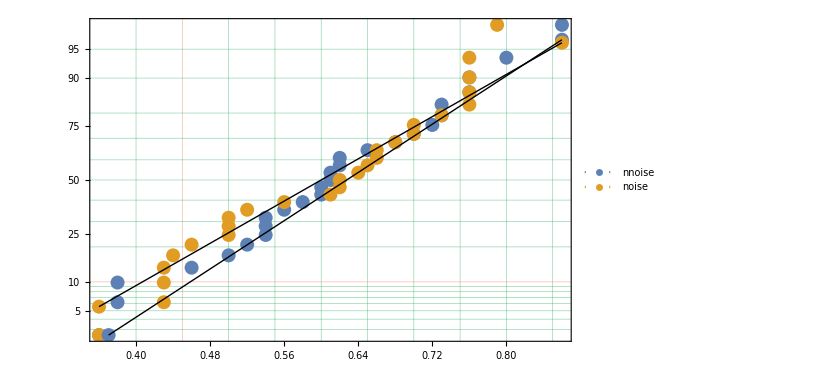

```mathematica
ProbabilityScalePlot[{noise[[2;;,1]],nnoise[[2;;,1]]},PlotLegends->{"nnoise","noise"}, GridLines->Automatic, GridLinesStyle->"Classic",PlotRange->Full]
```

```mathematica
δ=EstimatedDistribution[noise[[2;;,1]], NormalDistribution[μ,σ]]
```

NormalDistribution[0.607778,0.125973]

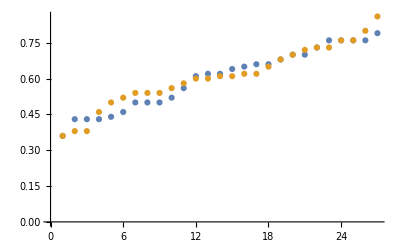

```mathematica
{Sort[nnoise[[2;;,1]]],Sort[noise[[2;;,1]]]}//ListPlot
```

```mathematica
RandomReal
```